```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210224_impacts_in_time_windows"];
```

```mathematica
datafull=Import["../data/ccm1_data_modified.csv",HeaderLines->2];
```

```mathematica
datafull[[1]]
```

{1,122,115686,CCM1,14.12.16,16000181-04,148956,#NAME?,1.24×10^6,87,2.74×10^9,3.35×10^9,16000181,26,0,0}

```mathematica
Dimensions@datafull
```

{459203,16}

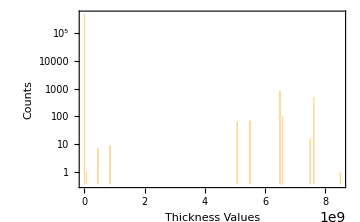
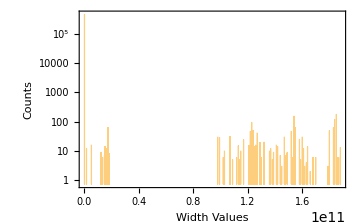

```mathematica
{Histogram[datafull[[All,10]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafull[[All,9]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium]}
```

```mathematica
datafullnoNA=datafull/."NA"->0;
```

```mathematica
thickpos=Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(#==2&)];
```

```mathematica
Length@thickpos
```

396299

```mathematica
datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[datafullnoNA[[Flatten@thickpos,9]]][[All,2]],_?(#==12&)]]],11]]="NA";
datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[datafullnoNA[[Flatten@thickpos,9]]][[All,2]],_?(#==12&)]]],12]]="NA";
datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[datafullnoNA[[Flatten@thickpos,9]]][[All,2]],_?(#==12&)]]],10]]="NA";
datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[datafullnoNA[[Flatten@thickpos,9]]][[All,2]],_?(#==12&)]]],9]]="NA";
```

```mathematica
datafullnoNA=datafullnoNA/."NA"->0.;
```

```mathematica
datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[datafullnoNA[[Flatten@thickpos,9]]][[All,2]],_?(#==7&)]]],11]]/=10^5;
datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[datafullnoNA[[Flatten@thickpos,9]]][[All,2]],_?(#==7&)]]],12]]/=10^5;
datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[datafullnoNA[[Flatten@thickpos,9]]][[All,2]],_?(#==7&)]]],9]]/=10^3;
```

```mathematica
density[thick_,width_,weight_,length_]:=N@weight/(thick*width*length)
```

```mathematica
(* KeySort@Counts@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[datafullnoNA[[Flatten@thickpos,9]]][[All,2]],_?(#≤4&)]]],9]] *)
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
```

```mathematica
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
KeySort@Counts@densities
```

<|-0.0003581→6,0→39,0.→7,17470,817.867→7,827.775→6|>
 |  |  |  |

```mathematica
RealDigits@7.397848389825049*^-7
```

{{7,3,9,7,8,4,8,3,8,9,8,2,5,0,4,9},-6}

```mathematica
N@density[76,1640,38400,40300]
```

7.64485×10^-6

```mathematica
table1=datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-13&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table1[[Flatten@Position[RealDigits[table1[[All,5]]][[All,2]],_?(#==5&)],1]],11]]*=10^8;
datafullnoNA[[table1[[Complement[Range@Length@table1,Flatten@Position[RealDigits[table1[[All,5]]][[All,2]],_?(#==5&)]],1]],12]]/=10^4;
datafullnoNA[[table1[[Complement[Range@Length@table1,Flatten@Position[RealDigits[table1[[All,5]]][[All,2]],_?(#==5&)]],1]],11]]*=10^4;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,17402,817.867→7,827.775→6|>
 |  |  |  |

```mathematica
table2=N@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-10&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table2[[Flatten@Position[RealDigits[table2[[All,5]]][[All,2]],_?(#==5&)],1]],11]]*=10^5;
datafullnoNA[[table2[[Complement[Range@Length@table2,Flatten@Position[RealDigits[table2[[All,5]]][[All,2]],_?(#==5&)]],1]],12]]/=10^5;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,17390,817.867→7,827.775→6|>
 |  |  |  |

```mathematica
table3=N@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-9&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table3[[Flatten@Position[RealDigits[table3[[All,5]]][[All,2]],_?(#==5&)],1]],11]]*=10^4;
datafullnoNA[[table3[[Complement[Range@Length@table3,Flatten@Position[RealDigits[table3[[All,5]]][[All,2]],_?(#==5&)]],1]],12]]/=10^5;
datafullnoNA[[table3[[Complement[Range@Length@table3,Flatten@Position[RealDigits[table3[[All,5]]][[All,2]],_?(#==5&)]],1]],11]]/=10;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,16268,817.867→7,827.775→6|>
 |  |  |  |

```mathematica
table4=N@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-8&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table4[[Flatten@Position[RealDigits[table4[[All,5]]][[All,2]],_?(#==4&)],1]],11]]*=10^3;
datafullnoNA[[table4[[Complement[Range@Length@table4,Flatten@Position[RealDigits[table4[[All,5]]][[All,2]],_?(#==4&)]],1]],12]]/=10^5;
datafullnoNA[[table4[[Complement[Range@Length@table4,Flatten@Position[RealDigits[table4[[All,5]]][[All,2]],_?(#==4&)]],1]],11]]/=10^2;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,16243,817.867→7,827.775→6|>
 |  |  |  |

```mathematica
RealDigits@3.91*^9
```

{{3,9,1,0,0,0,0,0,0,0,0,0,0,0,0,0},10}

```mathematica
table5=N@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-6&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table5[[Flatten@Position[RealDigits[table5[[All,5]]][[All,2]],_?(#==5&)],1]],11]]*=10;
datafullnoNA[[table5[[Flatten@Position[RealDigits[table5[[All,5]]][[All,2]],_?(#==6&)],1]],12]]/=10;
datafullnoNA[[table5[[Flatten@Position[RealDigits[table5[[All,5]]][[All,2]],_?(#==1&)],1]],11]]*=10^4;
datafullnoNA[[table5[[Flatten@Position[RealDigits[table5[[All,5]]][[All,2]],_?(#==1&)],1]],12]]*=10^3;
datafullnoNA[[table5[[Flatten@Position[RealDigits[table5[[All,5]]][[All,2]],_?(#==10&)],1]],11]]/=10^4;
datafullnoNA[[table5[[Flatten@Position[RealDigits[table5[[All,5]]][[All,2]],_?(#==10&)],1]],12]]/=10^5;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,16143,817.867→7,827.775→6|>
 |  |  |  |

```mathematica
table6=N@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-12&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table6[[Flatten@Position[RealDigits[table6[[All,5]]][[All,2]],_?(#==4&)],1]],11]]*=10^7;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,16142,817.867→7,827.775→6|>
 |  |  |  |

```mathematica
table7=N@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==3&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table7[[Flatten@Position[RealDigits[table7[[All,4]]][[All,2]],_?(#==5&)],1]],12]]*=10^8;
datafullnoNA[[table7[[Flatten@Position[RealDigits[table7[[All,4]]][[All,2]],_?(#==4&)],1]],12]]*=10^8;
datafullnoNA[[table7[[Flatten@Position[RealDigits[table7[[All,4]]][[All,2]],_?(#==10&)],1]],11]]/=10^5;
datafullnoNA[[table7[[Flatten@Position[RealDigits[table7[[All,4]]][[All,2]],_?(#==10&)],1]],12]]*=10^3;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,16062,0.766903→7,9.28829→24|>
 |  |  |  |

```mathematica
table8=N@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==0&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table8[[Flatten@Position[RealDigits[table8[[All,4]]][[All,2]],_?(#==5&)],1]],12]]*=10^5;
datafullnoNA[[table8[[Flatten@Position[RealDigits[table8[[All,4]]][[All,2]],_?(#==10&)],1]],11]]/=10^5;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,16041,0.0837549→7,9.28829→24|>
 |  |  |  |

```mathematica
RealDigits@0.07854014074393222
```

{{7,8,5,4,0,1,4,0,7,4,3,9,3,2,2,2},-1}

```mathematica
table9=N@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-1&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table9[[Flatten@Position[RealDigits[table9[[All,4]]][[All,2]],_?(#==5&)],1]],12]]*=10^4;datafullnoNA[[table9[[Flatten@Position[RealDigits[table9[[All,4]]][[All,2]],_?(#==4&)],1]],12]]*=10^4;
datafullnoNA[[table9[[Flatten@Position[RealDigits[table9[[All,4]]][[All,2]],_?(#==1&)],1]],11]]*=10^4;
datafullnoNA[[table9[[Flatten@Position[RealDigits[table9[[All,4]]][[All,2]],_?(#==1&)],1]],12]]*=10^8;
datafullnoNA[[table9[[Flatten@Position[RealDigits[table9[[All,4]]][[All,2]],_?(#==10&)],1]],11]]/=10^5;
datafullnoNA[[table9[[Flatten@Position[RealDigits[table9[[All,4]]][[All,2]],_?(#==10&)],1]],12]]/=10^1;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,15048,0.076598→3,9.28829→24|>
 |  |  |  |

```mathematica
table10=N@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-2&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table10[[Flatten@Position[RealDigits[table10[[All,4]]][[All,2]],_?(#==4&)],1]],12]]*=10^3;
datafullnoNA[[table10[[Flatten@Position[RealDigits[table10[[All,4]]][[All,2]],_?(#==3&)],1]],11]]*=10^1;datafullnoNA[[table10[[Flatten@Position[RealDigits[table10[[All,4]]][[All,2]],_?(#==3&)],1]],12]]*=10^4;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,15045,0.076598→3,9.28829→24|>
 |  |  |  |

```mathematica
table11=N@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-4&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table11[[Flatten@Position[RealDigits[table11[[All,4]]][[All,2]],_?(#==5&)],1]],12]]*=10^1;
datafullnoNA[[table11[[Flatten@Position[RealDigits[table11[[All,4]]][[All,2]],_?(#==1&)],1]],11]]*=10^3;datafullnoNA[[table11[[Flatten@Position[RealDigits[table11[[All,4]]][[All,2]],_?(#==1&)],1]],12]]*=10^4;datafullnoNA[[table11[[Flatten@Position[RealDigits[table11[[All,4]]][[All,2]],_?(#==10&)],1]],11]]/=10^6;
datafullnoNA[[table11[[Flatten@Position[RealDigits[table11[[All,4]]][[All,2]],_?(#==10&)],1]],12]]/=10^5;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,14507,0.076598→3,9.28829→24|>
 |  |  |  |

```mathematica
datafullnoNA[[Flatten@thickpos[[Flatten@Position[densities,0.00007550731477111845]]],11]]/=10^1;
datafullnoNA[[Flatten@thickpos[[Flatten@Position[densities,0.07659796061714341]]],11]]/=10^5;
datafullnoNA[[Flatten@thickpos[[Flatten@Position[densities,0.07659796061714341]]],12]]/=10^1;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,14507,0.000192284→7,9.28829→24|>
 |  |  |  |

```mathematica
Length@densities
Length@densities[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-5&)]]]
```

396299

396216

```mathematica
KeySort@Counts@densities[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-5&)]]]
```

<|1.03544×10^-6→5,1.15906×10^-6→7,14503,8.60358×10^-6→7|>
 |  |  |  |

suitable densities belong to rows that will be considered in the dataset

```mathematica
Length@Position[densities[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-5&)]]],_?(#>6*^-6&)]
```

396190

```mathematica
datafullnoNA[[Flatten@thickpos[[Complement[Range@Length@densities,Flatten@Position[densities[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-5&)]]],_?(#>6*^-6&)]]]],11]]="NA";
datafullnoNA[[Flatten@thickpos[[Complement[Range@Length@densities,Flatten@Position[densities[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-5&)]]],_?(#>6*^-6&)]]]],12]]="NA";
datafullnoNA[[Flatten@thickpos[[Complement[Range@Length@densities,Flatten@Position[densities[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-5&)]]],_?(#>6*^-6&)]]]],10]]="NA";
datafullnoNA[[Flatten@thickpos[[Complement[Range@Length@densities,Flatten@Position[densities[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-5&)]]],_?(#>6*^-6&)]]]],9]]="NA";
datafullnoNA=datafullnoNA/."NA"->0.;
```

```mathematica
datafullnoNA[[Complement[Range@Length@datafullnoNA,Flatten@Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(#≤2&)]],11]]="NA";
datafullnoNA[[Complement[Range@Length@datafullnoNA,Flatten@Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(#≤2&)]],12]]="NA";
datafullnoNA[[Complement[Range@Length@datafullnoNA,Flatten@Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(#≤2&)]],9]]="NA";
datafullnoNA[[Complement[Range@Length@datafullnoNA,Flatten@Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(#≤2&)]],10]]="NA";
datafullnoNA=datafullnoNA/."NA"->0.;
```

```mathematica
datafullnoNA[[Flatten@Position[datafullnoNA[[All,9]],_?(#>10^9&)],12]]="NA";
datafullnoNA[[Flatten@Position[datafullnoNA[[All,9]],_?(#>10^9&)],11]]="NA";
datafullnoNA[[Flatten@Position[datafullnoNA[[All,9]],_?(#>10^9&)],10]]="NA";
datafullnoNA[[Flatten@Position[datafullnoNA[[All,9]],_?(#>10^9&)],9]]="NA";
datafullnoNA=datafullnoNA/."NA"->0.;
```

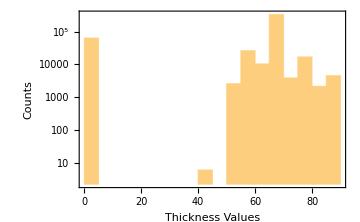
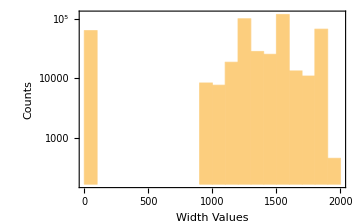
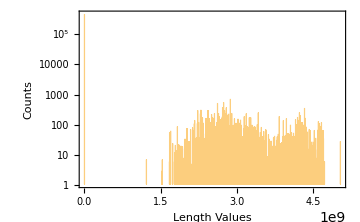
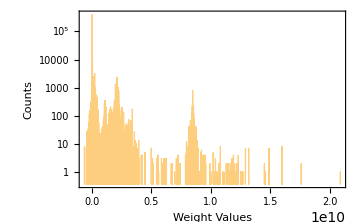

```mathematica
{Histogram[datafullnoNA[[All,10]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,9]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,12]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Length Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,11]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Weight Values","Counts"},ImageSize->Medium]}(*,Histogram[datafullnoNA[[All,12]],ScalingFunctions->"Log",PlotRange->{{0,10^7},All},Frame->True,FrameLabel->{"Length Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,11]],ScalingFunctions->"Log",PlotRange->{{-100,10^7},All},Frame->True,FrameLabel->{"Weight Values","Counts"},ImageSize->Medium]}*)
```

```mathematica
Length@Position[datafullnoNA[[All,10]],0]
Length@Position[datafullnoNA[[All,11]],0]
```

61327

10491

```mathematica
weightpos=Complement[Range@Length@datafullnoNA,Flatten@Join[Position[datafullnoNA[[All,10]],0],Position[datafullnoNA[[All,10]],0.]]];
```

```mathematica
KeySort@Counts[N@datafullnoNA[[weightpos,11]]];
```

```mathematica
datafullnoNA[[Flatten@weightpos[[Flatten@Position[RealDigits[datafullnoNA[[weightpos,11]]][[All,2]],_?(#==10&)]]],12]]/=10^6;
datafullnoNA[[Flatten@weightpos[[Flatten@Position[RealDigits[datafullnoNA[[weightpos,11]]][[All,2]],_?(#==10&)]]],11]]/=10^6;
```

```mathematica
datafullnoNA[[Flatten@weightpos[[Flatten@Position[RealDigits[datafullnoNA[[weightpos,11]]][[All,2]],_?(#==9&)]]],12]]/=10^5;
datafullnoNA[[Flatten@weightpos[[Flatten@Position[RealDigits[datafullnoNA[[weightpos,11]]][[All,2]],_?(#==9&)]]],11]]/=10^5;
```

```mathematica
datafullnoNA[[Flatten@weightpos[[Flatten@Position[RealDigits[datafullnoNA[[weightpos,11]]][[All,2]],_?(#==8&)]]],12]]/=10^4;
datafullnoNA[[Flatten@weightpos[[Flatten@Position[RealDigits[datafullnoNA[[weightpos,11]]][[All,2]],_?(#==8&)]]],11]]/=10^4;
```

```mathematica
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],2.6*^7]]],9]]="NA";
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],2.6*^7]]],10]]="NA";
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],2.6*^7]]],12]]="NA";
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],2.6*^7]]],11]]="NA";
datafullnoNA=datafullnoNA/."NA"->0.;
```

```mathematica
datafullnoNA[[weightpos[[Flatten@Position[RealDigits[datafullnoNA[[weightpos,11]]][[All,2]],_?(#==6&)]]],12]]/=10;
datafullnoNA[[weightpos[[Flatten@Position[RealDigits[datafullnoNA[[weightpos,11]]][[All,2]],_?(#==6&)]]],11]]/=10;
```

```mathematica
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(#≥26700&)]]],12]]/=10;
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(#≥26700&)]]],11]]/=10;
```

```mathematica
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(400≤#<2670&)]]],12]]*=10;
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(400≤#<2670&)]]],11]]*=10;
```

```mathematica
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(3<#<4&)]]],12]]*=1000;
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(3<#<4&)]]],11]]*=1000;
```

```mathematica
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(1<#<3&)]]],12]]*=10000;
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(1<#<3&)]]],11]]*=10000;
```

```mathematica
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(0.01<#<1&)]]],12]]*=1000000;
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(0.01<#<1&)]]],11]]*=1000000;
```

```mathematica
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(10^(-4)<#<0.01&)]]],12]]*=10^8;
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(10^(-4)<#<0.01&)]]],11]]*=10^8;
```

```mathematica
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(10^(-5)<#<10^(-4)&)]]],12]]*=10^9;
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(10^(-5)<#<10^(-4)&)]]],11]]*=10^9;
```

```mathematica
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?Negative]]],12]]*=10^7;
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?Negative]]],11]]*=-10^7;
```

```mathematica
datafullnoNA[[Flatten@Position[datafullnoNA[[All,12]],_?(#>80000&)],9]]="NA";
datafullnoNA[[Flatten@Position[datafullnoNA[[All,12]],_?(#>80000&)],10]]="NA";
datafullnoNA[[Flatten@Position[datafullnoNA[[All,12]],_?(#>80000&)],11]]="NA";
datafullnoNA[[Flatten@Position[datafullnoNA[[All,12]],_?(#>80000&)],12]]="NA";
datafullnoNA=datafullnoNA/."NA"->0.;
```

```mathematica
KeySort@Counts[N@datafullnoNA[[weightpos,11]]];
```

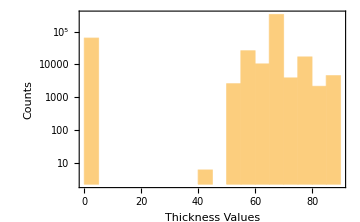
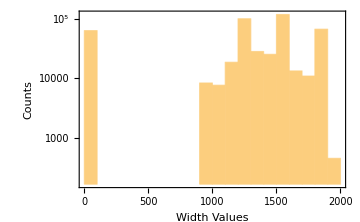
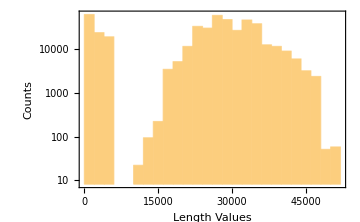
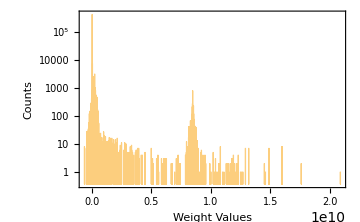

```mathematica
{Histogram[datafullnoNA[[All,10]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,9]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,12]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Length Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,11]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Weight Values","Counts"},ImageSize->Medium]}
```

```mathematica
Length@Position[datafullnoNA[[All,10]],0]
Length@Position[datafullnoNA[[All,11]],0]
```

61327

10491

```mathematica
weightposonzerosofothers=Intersection[Flatten@Position[datafullnoNA[[All,10]],0],Complement[Range@Length@datafullnoNA[[All,11]],Flatten@Join[Position[datafullnoNA[[All,11]],0],Position[datafullnoNA[[All,11]],0.]]]];
Length@weightposonzerosofothers
```

50843

```mathematica
RealDigits@-9.47*^7
```

{{9,4,7,0,0,0,0,0,0,0,0,0,0,0,0,0},8}

```mathematica
datafullnoNA[[weightposonzerosofothers[[Flatten@Position[RealDigits[datafullnoNA[[weightposonzerosofothers,11]]][[All,2]],_?(#==11&)]]],11]]/=10^6;
```

```mathematica
datafullnoNA[[weightposonzerosofothers[[Flatten@Position[RealDigits[datafullnoNA[[weightposonzerosofothers,11]]][[All,2]],_?(#==10&)]]],11]]/=10^6;
```

```mathematica
datafullnoNA[[weightposonzerosofothers[[Flatten@Position[RealDigits[datafullnoNA[[weightposonzerosofothers,11]]][[All,2]],_?(#==9&)]]],11]]/=10^5;
```

```mathematica
datafullnoNA[[weightposonzerosofothers[[Flatten@Position[datafullnoNA[[weightposonzerosofothers,11]],_?(5.3*^6≤#&)]]],11]]/=10^3;
```

```mathematica
datafullnoNA[[weightposonzerosofothers[[Flatten@Position[datafullnoNA[[weightposonzerosofothers,11]],_?(500000==#&)]]],11]]/=10^2;
```

```mathematica
datafullnoNA[[weightposonzerosofothers[[Flatten@Position[datafullnoNA[[weightposonzerosofothers,11]],_?(29000≤#&)]]],11]]/=10;
```

```mathematica
datafullnoNA[[weightposonzerosofothers[[Flatten@Position[datafullnoNA[[weightposonzerosofothers,11]],_?(1000<#<2700&)]]],11]]*=10;
```

```mathematica
datafullnoNA[[weightposonzerosofothers[[Flatten@Position[datafullnoNA[[weightposonzerosofothers,11]],_?(30.5≤#≤145&)]]],11]]*=100;
```

```mathematica
datafullnoNA[[weightposonzerosofothers[[Flatten@Position[datafullnoNA[[weightposonzerosofothers,11]],_?(3≤#≤25&)]]],11]]*=10^3;
```

```mathematica
datafullnoNA[[weightposonzerosofothers[[Flatten@Position[datafullnoNA[[weightposonzerosofothers,11]],_?(0.5≤#≤2.5&)]]],11]]*=10^4;
```

```mathematica
datafullnoNA[[weightposonzerosofothers[[Flatten@Position[datafullnoNA[[weightposonzerosofothers,11]],_?(-10*10^7<#≤-2.9*10^7&)]]],11]]/=-10^4;
```

```mathematica
datafullnoNA[[weightposonzerosofothers[[Flatten@Position[datafullnoNA[[weightposonzerosofothers,11]],_?(-2.6*10^7≤#≤-4.7*10^6&)]]],11]]/=-10^3;
```

```mathematica
datafullnoNA[[weightposonzerosofothers[[Flatten@Position[datafullnoNA[[weightposonzerosofothers,11]],_?(-6350≤#≤-2700&)]]],11]]*=-1;
```

```mathematica
datafullnoNA[[weightposonzerosofothers[[Flatten@Position[datafullnoNA[[weightposonzerosofothers,11]],_?(-2650≤#≤-1050&)]]],11]]*=-10;
```

```mathematica
datafullnoNA[[weightposonzerosofothers[[Flatten@Position[datafullnoNA[[weightposonzerosofothers,11]],_?(-4≤#≤-3&)]]],11]]*=-10^3;
```

```mathematica
datafullnoNA[[weightposonzerosofothers[[Flatten@Position[datafullnoNA[[weightposonzerosofothers,11]],_?(-2.5≤#≤-0.5&)]]],11]]*=-10^4;
```

```mathematica
datafullnoNA[[weightposonzerosofothers[[Flatten@Position[datafullnoNA[[weightposonzerosofothers,11]],_?(#==-0.147&)]]],11]]*=-10^5;
```

```mathematica
KeySort@Counts@datafullnoNA[[weightposonzerosofothers,11]];
```

```mathematica
datafullnoNA[[Flatten@Position[datafullnoNA[[All,11]],_?(#>150000&)],9]]="NA";
datafullnoNA[[Flatten@Position[datafullnoNA[[All,11]],_?(#>150000&)],10]]="NA";
datafullnoNA[[Flatten@Position[datafullnoNA[[All,11]],_?(#>150000&)],12]]="NA";
datafullnoNA[[Flatten@Position[datafullnoNA[[All,11]],_?(#>150000&)],11]]="NA";
datafullnoNA=datafullnoNA/."NA"->0.;
```

```mathematica
datafullnoNA[[Flatten@Position[datafullnoNA[[All,12]],9/200],9]]="NA";
datafullnoNA[[Flatten@Position[datafullnoNA[[All,12]],9/200],10]]="NA";
datafullnoNA[[Flatten@Position[datafullnoNA[[All,12]],9/200],11]]="NA";
datafullnoNA[[Flatten@Position[datafullnoNA[[All,12]],9/200],12]]="NA";
datafullnoNA=datafullnoNA/."NA"->0.;
```

```mathematica
datafullnoNA[[{390449,390450,390451,390452,390453,390454,390455},11]]=21200.;
datafullnoNA[[{390449,390450,390451,390452,390453,390454,390455},12]]=42200.;
```

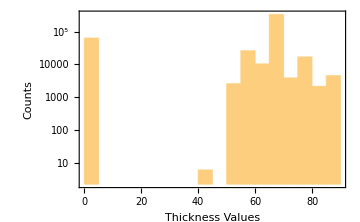
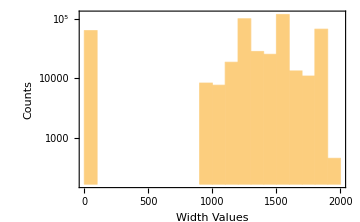
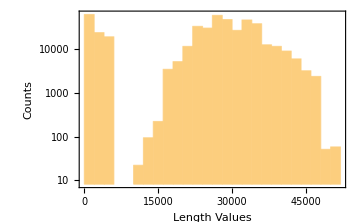
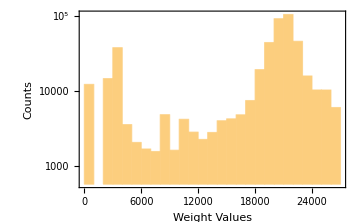

```mathematica
{Histogram[datafullnoNA[[All,10]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,9]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,12]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Length Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,11]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Weight Values","Counts"},ImageSize->Medium]}
```

```mathematica
datafullnoNA[[63;;69,9]]=1220.;
datafullnoNA[[63;;69,10]]=65;
datafullnoNA[[63;;69,12]]=6530./19700.*32600.;
```

```mathematica
Length@Position[datafullnoNA[[All,11]],0]
Length@Position[datafullnoNA[[All,12]],0]
Length@Position[datafullnoNA[[All,10]],0]
Length@Position[datafullnoNA[[All,9]],0]
```

10484

61320

61320

61320

```mathematica
thickvaluesthkpos=datafullnoNA[[All,10]];
widthvaluesthkpos=datafullnoNA[[All,9]];
weightvaluesthkpos=datafullnoNA[[All,11]];
lengthvaluesthkpos=datafullnoNA[[All,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.{Indeterminate->0,ComplexInfinity->0};
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|0→63079,1.15906×10^-6→7,1.34858×10^-6→7,3.3906×10^-6→7,6.78278×10^-6→10,6.85114×10^-6→8,6.87191×10^-6→3,6.87581×10^-6→6,6.88634×10^-6→8,6.91767×10^-6→7,6.92681×10^-6→7,6.93044×10^-6→7,6.94229×10^-6→8,14469,8.43639×10^-6→7,8.45417×10^-6→7,8.4573×10^-6→5,8.46265×10^-6→7,8.46572×10^-6→7,8.47446×10^-6→7,8.4763×10^-6→7,8.48076×10^-6→7,8.51343×10^-6→7,8.51626×10^-6→7,8.60324×10^-6→7,8.60358×10^-6→7,0.000192284→7|>
 |  |  |  |

```mathematica
datafullnoNA[[Flatten@Position[densities,0.00019228365685058598],9]]="NA";
datafullnoNA[[Flatten@Position[densities,0.00019228365685058598],10]]="NA";
datafullnoNA[[Flatten@Position[densities,0.00019228365685058598],11]]="NA";
datafullnoNA[[Flatten@Position[densities,0.00019228365685058598],12]]="NA";
datafullnoNA=datafullnoNA/."NA"->0.;
```

```mathematica
datafullnoNA[[Flatten@Position[densities,1.1590604621295158*^-6],9]]="NA";
datafullnoNA[[Flatten@Position[densities,1.1590604621295158*^-6],10]]="NA";
datafullnoNA[[Flatten@Position[densities,1.1590604621295158*^-6],11]]="NA";
datafullnoNA[[Flatten@Position[densities,1.1590604621295158*^-6],12]]="NA";
datafullnoNA=datafullnoNA/."NA"->0.;
```

```mathematica
datafullnoNA[[Flatten@Position[densities,1.3485812924803107*^-6],9]]="NA";
datafullnoNA[[Flatten@Position[densities,1.3485812924803107*^-6],10]]="NA";
datafullnoNA[[Flatten@Position[densities,1.3485812924803107*^-6],11]]="NA";
datafullnoNA[[Flatten@Position[densities,1.3485812924803107*^-6],12]]="NA";
datafullnoNA=datafullnoNA/."NA"->0.;
```

```mathematica
datafullnoNA[[Flatten@Position[densities,3.3905958651080047*^-6],9]]="NA";
datafullnoNA[[Flatten@Position[densities,3.3905958651080047*^-6],10]]="NA";
datafullnoNA[[Flatten@Position[densities,3.3905958651080047*^-6],11]]="NA";
datafullnoNA[[Flatten@Position[densities,3.3905958651080047*^-6],12]]="NA";
datafullnoNA=datafullnoNA/."NA"->0.;
```

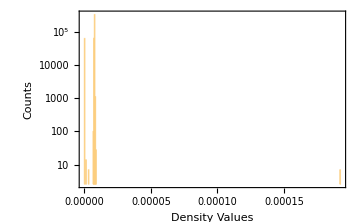

```mathematica
Histogram[densities,ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Density Values","Counts"},ImageSize->Medium]
```

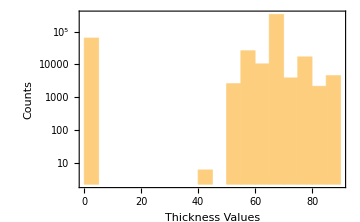
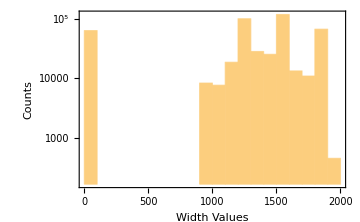
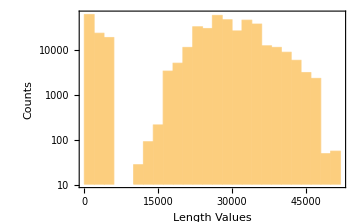
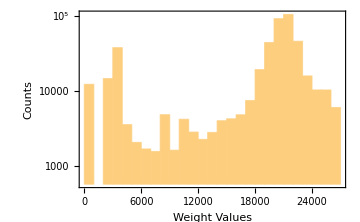

```mathematica
{Histogram[datafullnoNA[[All,10]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,9]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,12]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Length Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,11]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Weight Values","Counts"},ImageSize->Medium]}
```

```mathematica
convertionpos=Flatten@Position[datafullnoNA[[All,12]],_?(0<#<10000&)];
```

```mathematica
Position[datafullnoNA[[convertionpos,11]],_?(2669<#<4600&)];
```

```mathematica
KeySort@Counts@datafullnoNA[[convertionpos,12]];
```

```mathematica
KeySort@Counts@datafullnoNA[[convertionpos,11]];
```

```mathematica
datafullnoNA=datafullnoNA/. 0.->"NA";
```

```mathematica
(* Export["ccm_manipulated.csv",datafullnoNA] *)
```

ccm_manipulated.csv

```mathematica
manipulator[data_,seq_]:=Module[{initialdata,filtercon,part,pos,newwidth,newthick,firstlength,firstweight,newlength,newstgr},
initialdata=data;
filtercon=Select[initialdata,#[[13]]==seq&];
part=Join[filtercon[[All,1;;2]],filtercon[[All,9;;14]],2];
pos=Split[Select[Flatten@Take[Sort@If[MemberQ[part[[All,3]],0],Position[part[[All,3]],0],{}],All],part[[#,5]]!=0&],#2-#1==1&];
newwidth=Table[part[[pos[[i]][[1]]-1,3]],{i,Length@pos}];
newthick=Table[part[[pos[[i]][[1]]-1,4]],{i,Length@pos}];
firstlength=Table[part[[pos[[i]][[1]]-1,6]],{i,Length@pos}];
firstweight=Table[part[[pos[[i]][[1]]-1,5]],{i,Length@pos}];
newlength=Table[N@part[[pos[[i]][[1]],5]]*firstlength[[i]]/firstweight[[i]],{i,Length@pos}];
newstgr=Table[part[[pos[[i]][[1]]-1,8]],{i,Length@pos}];
Table[initialdata[[part[[pos[[i]],1]],9]]=newwidth[[i]],{i,Length@pos}];
Table[initialdata[[part[[pos[[i]],1]],10]]=newthick[[i]],{i,Length@pos}];
Table[initialdata[[part[[pos[[i]],1]],12]]=newlength[[i]],{i,Length@pos}];
Table[initialdata[[part[[pos[[i]],1]],14]]=newstgr[[i]],{i,Length@pos}];
initialdata]
```

```mathematica
datafullmodified=Import["../data/ccm_manipulated.csv",HeaderLines->1];
```

```mathematica
list=DeleteDuplicates@datafullmodified[[All,13]];
```

```mathematica
listo=Partition[list,Length@list/3];
```

```mathematica
a=listo[[1,1;;20]];
```

```mathematica
a
```

{16000181,17000341,17000281,17000761,17001141,17001201,17001221,16000201,17000401,17000381,17000421,17000441,17000021,17000261,16001121,16001141,16001201,16001181,16000761,16000781}

```mathematica
Position[datafullmodified[[All,10]],0]
```

{{45},{46},{47},{48},{98},{99},{100},{101},{102},{103},{104},{105},{149},{150},{151},{152},{153},{154},{199},{200},{201},{202},{203},{204},{205},{206},{207},{208},{209},{210},{262},{263},{264},{265},{266},{267},{268},{276},{277},{278},{279},{280},61236,{458853},{458854},{458855},{458943},{458944},{458945},{458946},{458947},{458948},{458949},{458975},{458976},{458977},{458978},{458979},{458980},{459077},{459078},{459079},{459080},{459081},{459082},{459083},{459084},{459113},{459114},{459115},{459116},{459117},{459118},{459154},{459155},{459156},{459157},{459158},{459159},{459176},{459177},{459178},{459179},{459202},{459203}}
 |  |  |  |

```mathematica
Fold[manipulator[datafullmodified,16000181],a]
```

{{1,122,115686,CCM1,14.12.16,16000181-04,148956,#NAME?,1240,87,2740,3350,16000181,26,0,0},{2,122,115686,CCM1,14.12.16,16000181-06,148958,#NAME?,1240,87,2740,3350,16000181,26,0,0},{3,122,115686,CCM1,14.12.16,16000181-07,148959,#NAME?,1240,87,2740,3350,16000181,26,0,0},{4,122,115686,CCM1,14.12.16,16000181-05,148957,#NAME?,1240,87,2740,3350,16000181,26,0,0},459196,{459201,4154,893030,CCM1,14.02.18,18024141-02,352650,#NAME?,NA,NA,NA,NA,18024141,41,0,5},{459202,154,120368,CCM1,03.01.17,0,0,0,0,0,0,0,0,0,0,0},{459203,154,120377,CCM1,03.01.17,0,0,0,0,0,0,0,0,0,0,0}}[1,8]
 |  |  |  |

```mathematica
%8[[41,42,43,44,45,46,47,48,95,96,97,98,99,100,101,102,103,104,105,106},{1,9,10,11,12}]]
```

Part::partw: Part {41,42,43,44,45,46,47,48,95,96,«10»} of «4471373880 bytes» does not exist.

$Aborted[]

```mathematica
Flatten[%8,20]
```

{{1,122,115686,CCM1,14.12.16,16000181-04,148956,#NAME?,1240,87,2740,3350,16000181,26,0,0},{2,122,115686,CCM1,14.12.16,16000181-06,148958,#NAME?,1240,87,2740,3350,16000181,26,0,0},{3,122,115686,CCM1,14.12.16,16000181-07,148959,#NAME?,1240,87,2740,3350,16000181,26,0,0},{4,122,115686,CCM1,14.12.16,16000181-05,148957,#NAME?,1240,87,2740,3350,16000181,26,0,0},{5,122,115686,CCM1,14.12.16,16000181-01,000000-1,#NAME?,1240,87,2740,3350,16000181,26,0,0},{6,122,115686,CCM1,14.12.16,16000181-02,148954,#NAME?,1240,87,2740,3350,16000181,26,0,0},{7,122,115686,CCM1,14.12.16,16000181-03,148955,#NAME?,1240,87,2740,3350,16000181,26,0,0},459190,{459198,4154,893030,CCM1,14.02.18,18024141-01,352649,#NAME?,NA,NA,NA,NA,18024141,41,0,5},{459199,4154,893030,CCM1,14.02.18,18024141-03,352651,#NAME?,NA,NA,NA,NA,18024141,41,0,5},{459200,4154,893030,CCM1,14.02.18,18024141-04,352652,#NAME?,NA,NA,NA,NA,18024141,41,0,5},{459201,4154,893030,CCM1,14.02.18,18024141-02,352650,#NAME?,NA,NA,NA,NA,18024141,41,0,5},{459202,154,120368,CCM1,03.01.17,0,0,0,0,0,0,0,0,0,0,0},{459203,154,120377,CCM1,03.01.17,0,0,0,0,0,0,0,0,0,0,0}}[16000181,17000341,17000281,14,16001181,16000761,16000781]
 |  |  |  |